# Homework 1

Name: Muhammad Salah Shatla

ID: 201500059

## Problem 1

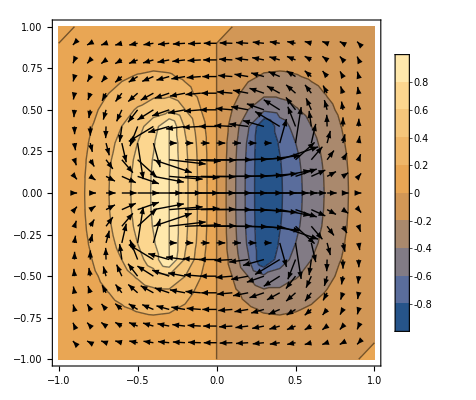

-Graphics3D-

```mathematica
ClearAll["Global`*"];


(*Initial Parameters*)
checkconvergence=10^-5; dx=.1; dy=.1; xstart=-1; xend=1;ystart=-1;yend=1;

(*Setting-up Initial Position Grid*)
xarray=Range[xstart,xend,dx]; lx=Length[xarray];
yarray=Range[ystart,yend,dy]; ly=Length[yarray];


(*Setting-up Initial Potential with Boundary*)
vxstart=ConstantArray[0.0,ly];
vxend=ConstantArray[0.0,ly];

vystart=ConstantArray[0.0,lx];
vyend=ConstantArray[0.0,lx];

vmat=ConstantArray[0.0,{lx,ly}];  (*The initial potential matrix*)
vold=vmat;

vmat[[All,1]]=vxstart;
vmat[[All,lx]]=vxend;

vmat[[1]]=vystart;
vmat[[ly]]=vyend;

(*Setting-up the Plates of the capacitor*)

(*Do[vmat[[i,0.8/dx]]=1;vmat[[i,1.4/dx]]=-1,{i,0.7/dy,1.5/dy}];*)

err=0.1;(*This parameter will change every iteration in the "While" loop untill it becomes ≤ the value of "checkconvergence"; this shows that the solution converged*)

While[err>checkconvergence,Do[If[i≥0.7/dy&&i≤1.5/dy,If[j==0.8/dx,vmat[[i,j]]=1,If[j==1.4/dx,vmat[[i,j]]=-1,vmat[[i]][[j]]=0.25(vmat[[i+1]][[j]]+vmat[[i-1]][[j]]+vmat[[i]][[j+1]]+vmat[[i]][[j-1]])]],vmat[[i]][[j]]=0.25(vmat[[i+1]][[j]]+vmat[[i-1]][[j]]+vmat[[i]][[j+1]]+vmat[[i]][[j-1]])],{i,2,lx-1},{j,2,lx-1}];err=Max[Abs[vmat-vold]];vold=vmat]

vmat//MatrixForm;

potentialfig=ListContourPlot[vmat,PlotLegends->Automatic,DataRange->{{-1.,1.},{-1.,1.}}];

ef={};
Do[efijx=(-(vmat[[i]][[j+1]]-vmat[[i]][[j-1]]))/(2 dx 15);efijy=(-(vmat[[i+1]][[j]]-vmat[[i-1]][[j]]))/(2 dy 15);ef=Append[ef,Arrow[{{-1+(i-1) dx,1-(j-1) dy},{-1+(i-1) dx+efijx,1-(j-1) dy+efijy}}]],{i,2,lx-1},{j,2,lx-1}];
fieldfig=Graphics[{ef}];

Show[{potentialfig,fieldfig}]

ListPlot3D[{vmat},AxesLabel->{"x","y","v"},PlotTheme-> "Scientific"]
```

## Problem 2

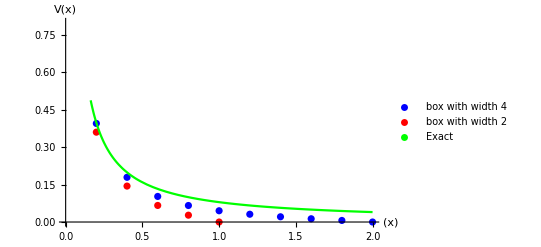

```mathematica
ClearAll["Global`*"];
dx = 0.2; dy = 0.2; dz=0.2; 
xstart=-2; xend=2;
x = Range[xstart,xend,dx];
y = Range[xstart,xend,dy];
z = Range[xstart,xend,dx];
vmat1=Table[0.0,{i,1,Length[x]},{j,1,Length[y]},{k,1,Length[z]}] ;
error=10;
While[ error>10^-5,
vold=vmat1;
Do[vmat1[[i]][[j]][[k]]=1/6(vmat1[[i+1,j,k]]+vmat1[[i-1,j,k]]+vmat1[[i,j,k+1]]+vmat1[[i,j,k-1]]+vmat1[[i,j+1,k]]+vmat1[[i,j-1,k]])+If[((i==j) && (j==k) && (i==Floor[Length[x]/2]+1)),1,0]/(6*dx),{i,2,Length[x]-1},{j,2,Length[y]-1},{k,2,Length[z]-1}];
 
error=Max[Abs[vmat1-vold]];

]
z0=Floor[Length[z]/2]+1;
vmat1=vmat1[[z0,z0,All]];
vx0=Table[{x[[i]],vmat1[[i]]},{i,Floor[Length[x]/2]+1,Length[x]}];
fig1=ListPlot[vx0,AxesLabel->{"x","vmat1"},PlotRange->{{0,2},{0,0.8}},PlotStyle->Blue,PlotLegends->PointLegend[{"box with width 4"}]];
(*--------------------------------------------------------*)

xstart=-1; xend=1;
x = Range[xstart,xend,dx];
y = Range[xstart,xend,dy];
z = Range[xstart,xend,dx];
vmat1=Table[0.0,{i,1,Length[x]},{j,1,Length[y]},{k,1,Length[z]}] ;
error=10;
While[ error>10^-5,
vold=vmat1;
Do[vmat1[[i]][[j]][[k]]=1/6(vmat1[[i+1,j,k]]+vmat1[[i-1,j,k]]+vmat1[[i,j,k+1]]+vmat1[[i,j,k-1]]+vmat1[[i,j+1,k]]+vmat1[[i,j-1,k]])+If[((i==j) && (j==k) && (i==Floor[Length[x]/2]+1)),1,0]/(6*dx),{i,2,Length[x]-1},{j,2,Length[y]-1},{k,2,Length[z]-1}];
 
error=Max[Abs[vmat1-vold]];

]
z1=Floor[Length[z]/2]+1;
vmat1=vmat1[[z1,z1,All]];
vx1=Table[{x[[i]],vmat1[[i]]},{i,Floor[Length[x]/2]+1,Length[x]}];
fig2=ListPlot[vx1,AxesLabel->{"x","vmat1"},PlotRange->{{0,2},{0,0.8}},PlotStyle->Red,PlotLegends->PointLegend[{"box with width 2"}]];

Show[fig1,fig2,Plot[1/(4π*r),{r,0,2},PlotLegends->PointLegend[{"Exact"}],PlotStyle->{Green,Thick}],AxesLabel->{"(x)","V(x)"}]
```

## Problem 3

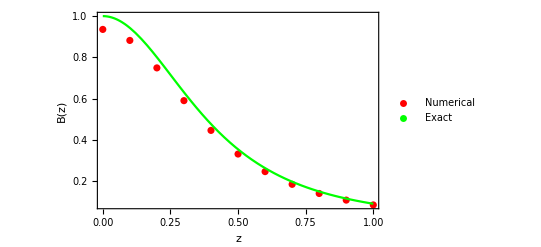

```mathematica
(* ΔB=1/(4 π)*(dr x L)/L^3*)

ClearAll["Global`*"];

dz=0.1;  
z= Range[0,1,dz];

B=0*z;
theta=Range[0,2π,(2π)/10];
r=0.5;

rmat=Table[0,{i,1,Length[theta]},{j,1,3}] ; 

 Do[rmat[[i]][[1]]=r*Cos[theta[[i]]];    
rmat[[i]][[2]]=r*Sin[theta[[i]]];
,{i,1,Length[theta]}];
 Do[
R={0,0,z[[j]]}; 

Do[

drmat= {(rmat[[i+1]][[1]]-rmat[[i]][[1]]),(rmat[[i+1]][[2]]-rmat[[i]][[2]]),0}; (*the z component is zero *)
L=R-rmat[[i]];
B[[j]]+= 1/(4 π)*(drmat[[1]]*L[[2]]-drmat[[2]]*L[[1]])/((√(r^2+z[[j]]^2))^3);
,{i,1,Length[rmat]-1}];
,{j,1,Length[B]}]
 bvsz= Table[{z[[i]],B[[i]]},{i,1,Length[z]}];
f1=ListPlot[bvsz,PlotStyle->Red,PlotLegends->PointLegend[{"Numerical"}],Frame->True];
 f2= Plot[r^2/(2*(r^2+zz^2)^(3/2)),{zz,0,1},PlotRange->All,PlotLegends->PointLegend[{"Exact"}],Frame->True,PlotStyle->Green];
Show[f1,f2,AxesOrigin->{0,0},PlotRange->All,FrameLabel->{"z","B(z)"}]
```